```mathematica
(*css zebrafinch model*)
ns := Na ba pa + Nn bn pn;
nh:= Na ba (1-pa) + Nn bn (1-pn);
NNa :=ns vs((1-lsO) vI z +lsO qO ) + nh vh((1-lhO) vI z +lhO qO );
NNn :=ns vs((1-lsO) vI (1-z)+lsO(1- qO) ) + nh vh((1-lhO) vI (1-z)+lhO(1- qO) );
qO := (1-u)(Na/(Na +Nn));
(*leave Q in matrix different than one up above recursions*)
```

```mathematica
AA:=({{0, 0, ba pa, bn pn}, {0, 0, ba(1-pa), bn(1-pn)}, {vs((1-lsO) vI z +lsO Q), vh((1-lhO) vI z +lhO Q ), 0, 0}, {vs((1-lsO) vI (1-z)+lsO(1- Q) ), vh((1-lhO) vI (1-z)+lhO(1- Q) ), 0, 0}})
```

```mathematica
NN = FullSimplify[NNn + NNa];
```

```mathematica
FFa=FullSimplify[NNa/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
FFn=FullSimplify[NNn/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
Simplify[FFn+FFa]
```

1

```mathematica
Fasols=Solve[FFa==Fa,Fa]
```

{{Fa→(bn lhO u vh-bn lhO pn u vh+bn vh vI-bn lhO vh vI-bn pn vh vI+bn lhO pn vh vI+bn lsO pn u vs+bn pn vI vs-bn lsO pn vI vs-ba vh vI z+bn vh vI z+ba lhO vh vI z-bn lhO vh vI z+ba pa vh vI z-ba lhO pa vh vI z-bn pn vh vI z+bn lhO pn vh vI z-ba pa vI vs z+ba lsO pa vI vs z+bn pn vI vs z-bn lsO pn vI vs z-√(-4 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs) (bn vh vI z-bn lhO vh vI z-bn pn vh vI z+bn lhO pn vh vI z+bn pn vI vs z-bn lsO pn vI vs z)+(-bn lhO u vh+bn lhO pn u vh-bn vh vI+bn lhO vh vI+bn pn vh vI-bn lhO pn vh vI-bn lsO pn u vs-bn pn vI vs+bn lsO pn vI vs+ba vh vI z-bn vh vI z-ba lhO vh vI z+bn lhO vh vI z-ba pa vh vI z+ba lhO pa vh vI z+bn pn vh vI z-bn lhO pn vh vI z+ba pa vI vs z-ba lsO pa vI vs z-bn pn vI vs z+bn lsO pn vI vs z)^2))/(2 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs))},{Fa→(bn lhO u vh-bn lhO pn u vh+bn vh vI-bn lhO vh vI-bn pn vh vI+bn lhO pn vh vI+bn lsO pn u vs+bn pn vI vs-bn lsO pn vI vs-ba vh vI z+bn vh vI z+ba lhO vh vI z-bn lhO vh vI z+ba pa vh vI z-ba lhO pa vh vI z-bn pn vh vI z+bn lhO pn vh vI z-ba pa vI vs z+ba lsO pa vI vs z+bn pn vI vs z-bn lsO pn vI vs z+√(-4 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs) (bn vh vI z-bn lhO vh vI z-bn pn vh vI z+bn lhO pn vh vI z+bn pn vI vs z-bn lsO pn vI vs z)+(-bn lhO u vh+bn lhO pn u vh-bn vh vI+bn lhO vh vI+bn pn vh vI-bn lhO pn vh vI-bn lsO pn u vs-bn pn vI vs+bn lsO pn vI vs+ba vh vI z-bn vh vI z-ba lhO vh vI z+bn lhO vh vI z-ba pa vh vI z+ba lhO pa vh vI z+bn pn vh vI z-bn lhO pn vh vI z+ba pa vI vs z-ba lsO pa vI vs z-bn pn vI vs z+bn lsO pn vI vs z)^2))/(2 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs))}}

```mathematica
subtest = {ba->3,bn->1,z->0.6,pa->0,pn->1,vs->0.8,vh->0.95,vI->0.7  ,lsO-> 0.2 ,lsV-> 0 ,lsI-> 0.8,lhO-> 0.8,lhI-> 0.2 ,u-> 0.1 };
```

```mathematica
Fasols[[1,1,2]]/.subtest (*check it is stable qhat with values, select positive q-hat*)
 Simplify[Fasols[[1,1,2]]/.{lhO->LHO,lhI -> LHI, lsO -> LSO, lsI-> LSI}](*copy and past solution below*)
 Fasols/.subtest
```

0.471384

(bn LHO u vh-bn LHO pn u vh+bn vh vI-bn LHO vh vI-bn pn vh vI+bn LHO pn vh vI+bn LSO pn u vs+bn pn vI vs-bn LSO pn vI vs-ba vh vI z+bn vh vI z+ba LHO vh vI z-bn LHO vh vI z+ba pa vh vI z-ba LHO pa vh vI z-bn pn vh vI z+bn LHO pn vh vI z-ba pa vI vs z+ba LSO pa vI vs z+bn pn vI vs z-bn LSO pn vI vs z-√(-4 bn vI ((-1+LHO) (-1+pn) vh-(-1+LSO) pn vs) (ba (LHO (-1+pa) vh (u-vI)+(-1+pa) vh vI-pa (LSO u+vI-LSO vI) vs)+bn (-LHO (-1+pn) vh (u-vI)+vh (vI-pn vI)+pn (LSO u+vI-LSO vI) vs)) z+(ba vI ((-1+LHO) (-1+pa) vh-(-1+LSO) pa vs) z+bn ((-1+pn) vh vI (1+z)+LHO (-1+pn) vh (u-vI (1+z))-pn vs (vI (1+z)+LSO (u-vI (1+z)))))^2))/(2 (ba (LHO (-1+pa) vh (u-vI)+(-1+pa) vh vI-pa (LSO u+vI-LSO vI) vs)+bn (-LHO (-1+pn) vh (u-vI)+vh (vI-pn vI)+pn (LSO u+vI-LSO vI) vs)))

{{Fa→0.471384},{Fa→-3.49838}}

```mathematica
QHAT[LHO_,LSO_] :=(bn LHO u vh-bn LHO pn u vh+bn vh vI-bn LHO vh vI-bn pn vh vI+bn LHO pn vh vI+bn LSO pn u vs+bn pn vI vs-bn LSO pn vI vs-ba vh vI z+bn vh vI z+ba LHO vh vI z-bn LHO vh vI z+ba pa vh vI z-ba LHO pa vh vI z-bn pn vh vI z+bn LHO pn vh vI z-ba pa vI vs z+ba LSO pa vI vs z+bn pn vI vs z-bn LSO pn vI vs z-√(-4 bn vI ((-1+LHO) (-1+pn) vh-(-1+LSO) pn vs) (ba (LHO (-1+pa) vh (u-vI)+(-1+pa) vh vI-pa (LSO u+vI-LSO vI) vs)+bn (-LHO (-1+pn) vh (u-vI)+vh (vI-pn vI)+pn (LSO u+vI-LSO vI) vs)) z+(ba vI ((-1+LHO) (-1+pa) vh-(-1+LSO) pa vs) z+bn ((-1+pn) vh vI (1+z)+LHO (-1+pn) vh (u-vI (1+z))-pn vs (vI (1+z)+LSO (u-vI (1+z)))))^2))/(2 (ba (LHO (-1+pa) vh (u-vI)+(-1+pa) vh vI-pa (LSO u+vI-LSO vI) vs)+bn (-LHO (-1+pn) vh (u-vI)+vh (vI-pn vI)+pn (LSO u+vI-LSO vI) vs)));
```

```mathematica
AA
AA2=AA/.{Q->Qh}
```

{{0,0,ba pa,bn pn},{0,0,ba (1-pa),bn (1-pn)},{vs (lsO Q+(1-lsO) vI z),vh (lhO Q+(1-lhO) vI z),0,0},{vs (lsO (1-Q)+(1-lsO) vI (1-z)),vh (lhO (1-Q)+(1-lhO) vI (1-z)),0,0}}

{{0,0,ba pa,bn pn},{0,0,ba (1-pa),bn (1-pn)},{vs (lsO Qh+(1-lsO) vI z),vh (lhO Qh+(1-lhO) vI z),0,0},{vs (lsO (1-Qh)+(1-lsO) vI (1-z)),vh (lhO (1-Qh)+(1-lhO) vI (1-z)),0,0}}

```mathematica
AA3=AA2;
```

```mathematica
AA4=AA3; (*make cues 100% reliable to simplify solution*)
```

```mathematica
LL=Eigenvalues[AA4];
```

```mathematica
LL/.subtest /. Qh -> 0.5
```

{0.-0.237681 ⅈ,0.+0.237681 ⅈ,-1.30196,1.30196}

```mathematica
Simplify[LL[[4]]]/.Qh->  QHAT[LHO,LSO];
```

```mathematica
(*isolate Dominant eigenvalue, substitute in q-hat*)
Lambda1[ lsO_, lhO_,LHO_,LSO_]:= Simplify[LL[[4]]]/.Qh->  QHAT[LHO,LSO];
```

```mathematica
(*take partial derivatives, substitute mutant for common type*)
DlsO=D[Lambda1[lsO, lhO,LHO,LSO],lsO]/. {LHO -> lhO,LSO-> lsO};
```

```mathematica
DlhO=D[Lambda1[lsO, lhO,LHO,LSO],lhO]/. {LHO -> lhO,LSO-> lsO};
```

```mathematica
(*try and graph*)

lsOstart=0.01;
lhOstart=0.01;
imax=500;
lsItab=Table[0,{i,imax}];
lhItab=Table[0,{i,imax}];
lsOtab=Table[0,{i,imax}];
lhOtab=Table[0,{i,imax}];
DlsOtab=Table[0,{i,imax}];
DlhOtab=Table[0,{i,imax}];
delta=0.04;
sub2={ba->3,bn->1,z->.9,vs->0.1,vh->0.9,vI->0.8  ,u->0.15 , pa -> 0.1, pn-> 0.9};
lsOtab[[1]]=lsOstart;
lhOtab[[1]]=lhOstart;

DlsOtab[[1]]=DlsO/.sub2/.{lsO->lsOstart,lhO->lhOstart};
DlhOtab[[1]]=DlhO/.sub2/.{lsO->lsOstart,lhO->lhOstart};
```

```mathematica
For[i=2,i<imax,i++,{

lsOtab[[i]]=lsOtab[[i-1]]  + delta DlsO/.sub2/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsOtab[[i]]=If[lsOtab[[i]]>1,1,lsOtab[[i]]];
lsOtab[[i]]=If[lsOtab[[i]]<0,0,lsOtab[[i]]];

lhOtab[[i]]=lhOtab[[i-1]]  + delta DlhO/.sub2/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhOtab[[i]]=If[lhOtab[[i]]>1,1,lhOtab[[i]]];
lhOtab[[i]]=If[lhOtab[[i]]<0,0,lhOtab[[i]]];

DlsOtab[[i]]=DlsO/.sub2/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlhOtab[[i]]=DlhO/.sub2/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
}];
```

```mathematica
lsItab = 1-lsOtab;
lhItab = 1-lhOtab;
```

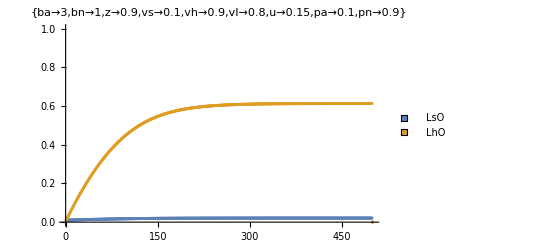

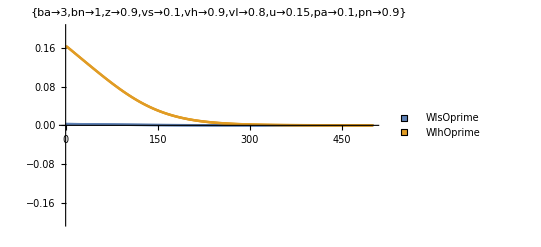

```mathematica
ListPlot[{lsOtab,lhOtab},PlotRange->{All,{0,1}},PlotLegends->PointLegend[{LsO,LhO},LegendMarkers->Graphics[Rectangle[]]],PlotLabel->sub2] 
ListPlot[{DlsOtab,DlhOtab},PlotRange->{All,{-0.2,0.2}},PlotLegends->PointLegend[{WlsOprime,WlhOprime},LegendMarkers->Graphics[Rectangle[]]],PlotLabel->sub2]
```